```mathematica
BasicEntropy[p_] := -p*Log[2, p]
```

```mathematica
TransmittedInformation[{{pys_, pyw_}, {pns_, pnw_}}] := 
  BasicEntropy[pys + pyw] + BasicEntropy[pns + pnw] + BasicEntropy[pys + pns] + 
    BasicEntropy[pyw + pnw] - BasicEntropy[pys] - BasicEntropy[pyw] - BasicEntropy[pns] - 
    BasicEntropy[pnw]
(*This is the transinformation aka mutual information in a 2x2 joint probability*)
```

```mathematica
RestrictedInformation[a_, b_, p_] := 
TransmittedInformation[{{a*p, b*(1 - p)}, {(1 - a)*p, (1-b)*(1 - p)}}]
(*a 2x2 joint probability is four nonnegative numbers that satisfy the constraint that they
sum to 1; this leaves three free variables. We can parameterize this as the probability p
that there is a signal, and conditional probabilities b that given a signal the receiver says
yes and the probability a that given no signal the receiver says yes*)
```

```mathematica
RestrictedInformation[.4, .6, .5]
```

0.0290494

```mathematica
ImplicitContourDerivative[a_,b_,p_]=-Simplify[D[RestrictedInformation[a,b,p],a]]/
   Simplify[D[RestrictedInformation[a,b,s],b]];
(*basic multivariable calculus tells us that the slope of a level contour of a function 
f(a,b) is given by the differential equation db/da=-((∂f/∂a)/(∂f/∂b)); in our case the amounts to the nonlinear differential equation 
db/da=-(s Log[(a/(1-a))(((1-b)+(b-a) s)/(b-(b-a) s)) ])/((1-s) (Log[(b/(1-b))(((1-b)+(b-a) s)/(b-(b-a) s)) ]))*)
```

```mathematica
bprime[a_,s_]:=ImplicitContourDerivative[a,b[a],s]
bNprime[a_,b_,n_,s_]:=bNprime[a,b,n,s]=(D[bNprime[a,b,n-1,s]/.b->b[a],a]/.b'[a]->bprime[a,s])/.b[a]->b
bNprime[a,b,1,s]:=bprime[a,s]/.b[a]->b
(*this is the mathematica expression of the nonlinear differential equation above*)
```

```mathematica
TaylorCoefficient[x0_,y0_,n_,s0_]:=bNprime[a,b,n,s]/n!/.{a->x0,b->y0,s->s0}
TaylorSeries[x_,x0_,y0_,n_,s_]:=y0+Sum[TaylorCoefficient[x0,y0,k,s]*(x-x0)^k,{k,1,n}]
(*This function gives a Taylor series approximation of the isoinformation contour that passes through the point x0,y0*)
```

Above is "mathematica" code for a function which gives the nth order Taylor series approximation to that isoinformation contour of the transmitted information function which passes through the point (x0,y0) when the probability of a "signal" is "s", while the probability of merely noise is "1-s".  This code can be memory intensive, you are advised allocate sufficient memory to the task, and/or to start with "n" small and work up to larger values.  Below are: 1) Numerically computed contours, 2) a fifth order Taylor approximation to the isoinformation contour and 3) A plot of this approximation, all in the case that "s"=.5.  BE AWARE that these approximations will always give inaccurate results near where the isoinformation contour intersects the lines x=0, x=1, y=0, y=1.

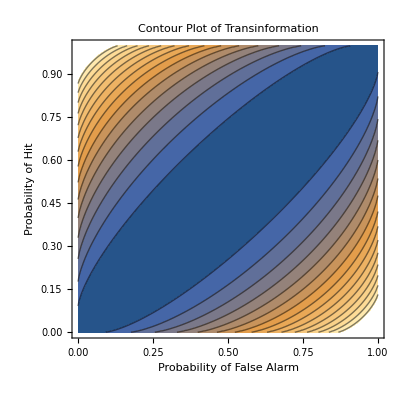

```mathematica
ContourPlot[RestrictedInformation[a, b, .5], {a, 0.0001, .9999}, {b, 0.0001, .9999}, 
  PlotPoints -> 50, Contours -> 20,PlotLabel->"Contour Plot of Transinformation",FrameLabel->{"Probability of False Alarm","Probability of Hit" }]
(*Below is a contour plot of the transinformation, the contours being the isoinformation curves*)
```

```mathematica
TaylorSeries[x,.25,.75,5,.5]
RestrictedInformation[.25, .75, .5]
(*this uses the fifth order Taylor polynomial to compute an approximation of the contour that passes through the point a=.25, b=.75 when p=.5. The transinformation for this case is 0.188722*)
```

0.75+1. (-0.25+x)-1.21365 (-0.25+x)^2+1.47295 (-0.25+x)^3-3.80799 (-0.25+x)^4+9.52554 (-0.25+x)^5

0.188722

```mathematica
f[x_]:=0.75+1. (-0.25+x)-1.2136523021691166 (-0.25+x)^2+1.4729519105603963 (-0.25+x)^3-3.8079867959311535 (-0.25+x)^4+9.525541162887286 (-0.25+x)^5
(*we encapsulate the Taylor polynomial above as a function f(x)*)
```

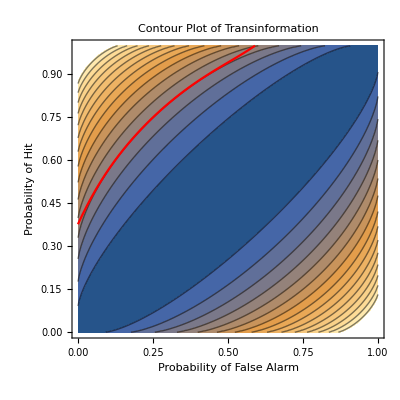

```mathematica
Show[ContourPlot[RestrictedInformation[a, b, .5], {a, 0.0001, .9999}, {b, 0.0001, .9999}, 
  PlotPoints -> 50, Contours -> 20,PlotLabel->"Contour Plot of Transinformation",FrameLabel->{"Probability of False Alarm","Probability of Hit" }],Plot[f[x],{x,0,.75},PlotRange->{0,1},AspectRatio->1,Frame->True,PlotStyle->Red]]
(*Here we lay the Taylor polynomial approximation to the contour in red on top of the contours portrayed above. We see that, as promised, the Taylor polynomial is quite close to the contour near the point (.25,.75), but diverges significantly as the contour nears x=0 and near y=1*)
```

```mathematica
(*The right hand side of the differential equation representing contours is just below*)
(p/(1-p))(Log[(a/(1-a))]-Log[(b(1-p)+a p)/(1-b (1-p)-a p)])/(Log[(b/(1-b))]-Log[(b(1-p)+a p)/(1-b (1-p)-a p)])
(*when p=1/2 this amounts to the following*)
```

```mathematica
-(Log[a/(1-a)]-Log[(0.5 a+0.5 b[a])/(1-0.5 a-0.5 b[a])])/(Log[b[a]/(1-b[a])]-Log[(0.5 a+0.5 b[a])/(1-0.5 a-0.5 b[a])])
```

```mathematica
(*here we obtain a numerical approximation of the differential equation; there are some computational difficulties near where the contour encounters conditional probabilities of 0 or 1 but the numerics are robust enough that useful results are obtained anyway*)
q=NDSolve[{b'[a]==-(Log[a/(1-a)]-Log[(0.5 a+0.5 b[a])/(1-0.5 a-0.5 b[a])])/(Log[b[a]/(1-b[a])]-Log[(0.5 a+0.5 b[a])/(1-0.5 a-0.5 b[a])]),b[0.25]==.75},b[a],{a,0,.75}]
```

{{b[a]→                                  -6
InterpolatingFunction[{{1.37063 10  , 0.671017}}, <>][a]}}

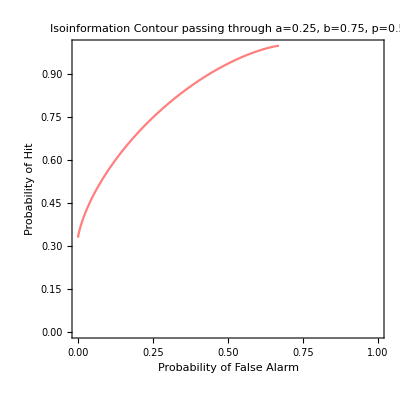

```mathematica
plt=Plot[Evaluate[b[a]/.q],{a,0,1},PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->{Opacity[.5],Red},Frame->True,PlotLabel->"Isoinformation Contour passing through a=0.25, b=0.75, p=0.5",FrameLabel->{"Probability of False Alarm","Probability of Hit" }]
```

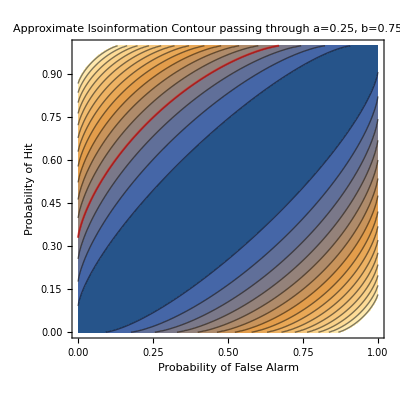

```mathematica
Show[ContourPlot[RestrictedInformation[a, b, .5], {a, 0.0001, .9999}, {b, 0.0001, .9999}, 
  PlotPoints -> 50, Contours -> 20,PlotLabel->"Approximate Isoinformation Contour passing through a=0.25, b=0.75, p=0.5",FrameLabel->{"Probability of False Alarm","Probability of Hit" }],plt]
(*Here we lay the p=0.5 numerical approximation to the contour in red on top of the contours portrayed above. We see that the numerical approximation is more faithful to the correct contour than the Taylor polynomial*)
```

```mathematica
(p/(1-p))(Log[(a/(1-a))]-Log[(b(1-p)+a p)/(1-b (1-p)-a p)])/(Log[(b/(1-b))]-Log[(b(1-p)+a p)/(1-b (1-p)-a p)])/.p->0.9
```

(9. (Log[a/(1-a)]-Log[(0.9 a+0.1 b)/(1-0.9 a-0.1 b)]))/(-Log[(0.9 a+0.1 b)/(1-0.9 a-0.1 b)]+Log[b/(1-b)])

```mathematica
q1=NDSolve[{b'[a]==-(9(Log[a/(1-a)]-Log[(0.9 a+0.1 b[a])/(1-0.9 a-0.1 b[a])]))/(Log[b[a]/(1-b[a])]-Log[(0.9 a+0.1 b[a])/(1-0.9 a-0.1 b[a])]),b[0.25]==.75},b[a],{a,0,.75}]
```

{{b[a]→                                 -7
InterpolatingFunction[{{3.3058 10  , 0.594662}}, <>][a]}}

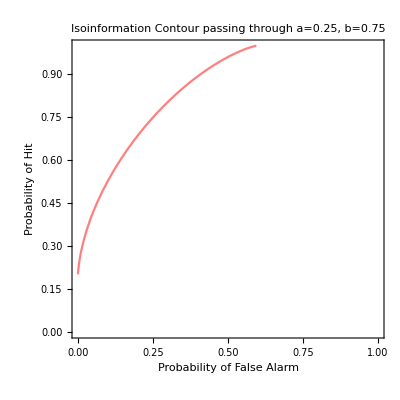

```mathematica
plt1=Plot[Evaluate[b[a]/.q1],{a,0,1},PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->{Opacity[.5],Red},Frame->True,PlotLabel->"Isoinformation Contour passing through a=0.25, b=0.75",FrameLabel->{"Probability of False Alarm","Probability of Hit" }]
```

```mathematica
Show[ContourPlot[RestrictedInformation[a, b, .9], {a, 0.0001, .9999}, {b, 0.0001, .9999}, 
  PlotPoints -> 50, Contours -> 20,PlotLabel->"Contour Plot of Transinformation p =0.9",FrameLabel->{"Probability of False Alarm","Probability of Hit" }],plt1]
(*Here we lay the p=0.9 numerical approximation to the contour in red on top of the contours portrayed above. We see that the numerical approximation while faithful to the correct contour is noticably skew*)
```

-Graphics-